# PROBLEM SHEET 06

## LAB REPORT BY RAFSAN AL MAMUN

```mathematica
DSolve[y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve[x^2*y'[x]==y[x]-y[x]*x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/E},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[y''[x]+5y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

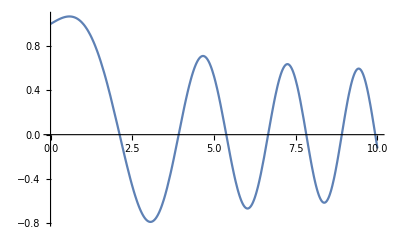

```mathematica
Plot[Evaluate[y[x]/.a],{x,0,10}]
```

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[…][t]}}

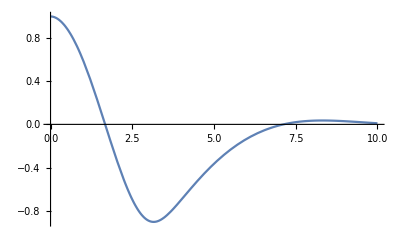

```mathematica
Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
c=NDSolve[{y''[x]+0.3y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y[x],{x,0,30}]
```

{{y[x]→InterpolatingFunction[…][x]}}

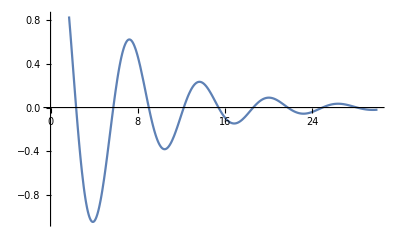

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
```

```mathematica
DSolve[L*Q''[t]+R*Q'[t]+1/C*Q[t]==Subscript[V, 0]*E^(j*w*t),Q[t],t]
```

{{Q[t]→ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t) C[1]+ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t) C[2]-(2 C L (√C ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R-√C ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R+ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w-2 √C ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w) V_0)/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))}}

```mathematica
DSolve[L*i'[t]+R*i[t]+(i[t])^2/(2C)==Subscript[V, 0]*E^(j*w*t),i[t],t]
```

{{i[t]→(2 C L (-(ⅈ^(R/(j L w)) ⅇ^(-(R t)/(2 L)) R BesselI[R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)] Gamma[1+R/(j L w)])/(2 L)+1/(2 √2 √C L √(ⅇ^(j t w) V_0))ⅈ^(R/(j L w)) ⅇ^(-(R t)/(2 L)+j t w) (BesselI[-1+R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)]+BesselI[1+R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)]) Gamma[1+R/(j L w)] V_0+C[1] (-(ⅈ^(-R/(j L w)) ⅇ^(-(R t)/(2 L)) R BesselI[-R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)] Gamma[1-R/(j L w)])/(2 L)+1/(2 √2 √C L √(ⅇ^(j t w) V_0))ⅈ^(-R/(j L w)) ⅇ^(-(R t)/(2 L)+j t w) (BesselI[-1-R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)]+BesselI[1-R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)]) Gamma[1-R/(j L w)] V_0)))/(ⅈ^(-R/(j L w)) ⅇ^(-(R t)/(2 L)) BesselI[-R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)] C[1] Gamma[1-R/(j L w)]+ⅈ^(R/(j L w)) ⅇ^(-(R t)/(2 L)) BesselI[R/(j L w),(√2 √(ⅇ^(j t w) V_0))/(√C j L w)] Gamma[1+R/(j L w)])}}